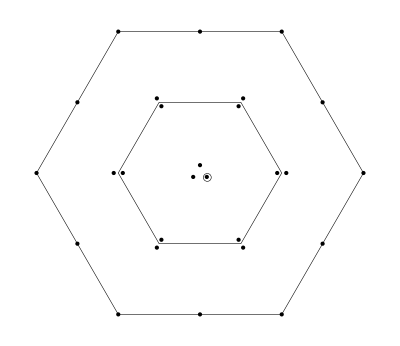

Y=0,  I_3=0

(ud+du)(ūd̄+d̄ū)-(us+su)(ūs̄+s̄ū)-ddd̄d̄+sss̄s̄

```mathematica
(*-------------------------------*)
```

The current J:

(d_a^T C σ^αμ d_b) ((d̄)_b σ^αμ C((d̄)_a)^T-(d̄)_a σ^αμ C((d̄)_b)^T)+(d_a^T C σ^αμ u_b) ((d̄)_a σ^αμ C((ū)_b)^T-(d̄)_b σ^αμ C((ū)_a)^T)+(u_a^T C σ^αμ d_b) ((d̄)_a σ^αμ C((ū)_b)^T-(d̄)_b σ^αμ C((ū)_a)^T)+(d_a^T C σ^αμ u_b) ((ū)_a σ^αμ C((d̄)_b)^T-(ū)_b σ^αμ C((d̄)_a)^T)+(u_a^T C σ^αμ d_b) ((ū)_a σ^αμ C((d̄)_b)^T-(ū)_b σ^αμ C((d̄)_a)^T)+(s_a^T C σ^αμ s_b) ((s̄)_a σ^αμ C((s̄)_b)^T-(s̄)_b σ^αμ C((s̄)_a)^T)+(s_a^T C σ^αμ u_b) ((s̄)_b σ^αμ C((ū)_a)^T-(ū)_a σ^αμ C((s̄)_b)^T)+(u_a^T C σ^αμ s_b) ((s̄)_b σ^αμ C((ū)_a)^T-(ū)_a σ^αμ C((s̄)_b)^T)+(s_a^T C σ^αμ u_b) ((ū)_b σ^αμ C((s̄)_a)^T-(s̄)_a σ^αμ C((ū)_b)^T)+(u_a^T C σ^αμ s_b) ((ū)_b σ^αμ C((s̄)_a)^T-(s̄)_a σ^αμ C((ū)_b)^T)

the Fierz rearranged J (to naively get the decay partten)

```mathematica
-6 (d̄(γ̄)^5 d d̄(γ̄)^5 d)-d̄ σ^μν d d̄ σ^μν d+12 (ū(γ̄)^5 u) (d̄(γ̄)^5 d-s̄(γ̄)^5 s)+12 (ū 1u) (d̄ 1d-s̄ 1s)+12 (d̄(γ̄)^5 u ū(γ̄)^5 d)+2 (d̄ σ^μν d ū σ^μν u)+2 (d̄ σ^μν u ū σ^μν d)+12 (d̄ 1u ū 1d)-6 (d̄ 1d d̄ 1d)+6 (s̄(γ̄)^5 s s̄(γ̄)^5 s)+s̄ σ^μν s s̄ σ^μν s-12 (s̄(γ̄)^5 u ū(γ̄)^5 s)-2 (s̄ σ^μν s ū σ^μν u)-2 (s̄ σ^μν u ū σ^μν s)-12 (s̄ 1u ū 1s)+6 (s̄ 1s s̄ 1s)
```

Π(q^2)=
-(log(-q^2/μ^2) q^8)/(64 π^6)-(5 ⟨ GG ⟩ log(-q^2/μ^2) q^4)/(24 π^5)-(3 ⟨ d̄ d⟩ log(-q^2/μ^2) m_d q^4)/π^4-(3 ⟨ s̄ s⟩ log(-q^2/μ^2) m_s q^4)/π^4-(4 ⟨ ū u⟩ log(-q^2/μ^2) m_u q^4)/π^4-(48 ⟨ d̄ d⟩^2 log(-q^2/μ^2) q^2)/π^2-(48 ⟨ s̄ s⟩^2 log(-q^2/μ^2) q^2)/π^2-(48 ⟨ ū u⟩^2 log(-q^2/μ^2) q^2)/π^2+(5 ⟨G^3⟩ log(-q^2/μ^2) q^2)/(8 π^6)+(48 ⟨ d̄ d⟩ ⟨ s̄ s⟩ log(-q^2/μ^2) q^2)/π^2+(48 ⟨ d̄ d⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/π^2+(48 ⟨ s̄ s⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/π^2+(16 ⟨ d̄ d⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/π^2-(8 ⟨ s̄ s⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/π^2-(8 ⟨ ū u⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/π^2-(8 ⟨ d̄ d⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/π^2+(16 ⟨ s̄ s⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/π^2-(8 ⟨ ū u⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/π^2-(8 ⟨ d̄ d⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/π^2-(8 ⟨ s̄ s⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/π^2+(16 ⟨ ū u⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/π^2-(16 ⟨ GG ⟩ ⟨ d̄ d⟩^2)/(π q^2)-(16 ⟨ GG ⟩ ⟨ s̄ s⟩^2)/(π q^2)-(16 ⟨ GG ⟩ ⟨ ū u⟩^2)/(π q^2)-⟨ d̄ Gd⟩^2/(3 π^2 q^2)-⟨ s̄ Gs⟩^2/(3 π^2 q^2)-⟨ ū Gu⟩^2/(3 π^2 q^2)+(16 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ s̄ s⟩)/(π q^2)+(16 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ ū u⟩)/(π q^2)+(16 ⟨ GG ⟩ ⟨ s̄ s⟩ ⟨ ū u⟩)/(π q^2)+(⟨ d̄ Gd⟩ ⟨ s̄ Gs⟩)/(3 π^2 q^2)+(⟨ d̄ Gd⟩ ⟨ ū Gu⟩)/(3 π^2 q^2)+(⟨ s̄ Gs⟩ ⟨ ū Gu⟩)/(3 π^2 q^2)-(448 ⟨ d̄ d⟩^3 m_d)/(3 q^2)-(320 ⟨ d̄ d⟩ ⟨ ū u⟩^2 m_d)/(3 q^2)-(448 ⟨ s̄ s⟩^3 m_s)/(3 q^2)-(320 ⟨ s̄ s⟩ ⟨ ū u⟩^2 m_s)/(3 q^2)+(32 ⟨ d̄ d⟩^2 ⟨ ū u⟩ (36 m_d-10 m_u))/(3 q^2)+(32 ⟨ s̄ s⟩^2 ⟨ ū u⟩ (36 m_s-10 m_u))/(3 q^2)+(384 ⟨ d̄ d⟩ ⟨ s̄ s⟩ ⟨ ū u⟩ m_u)/q^2

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for ρ_6=ρ_8=ρ_10=1

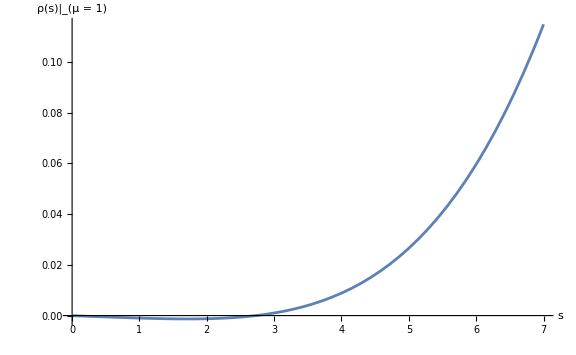
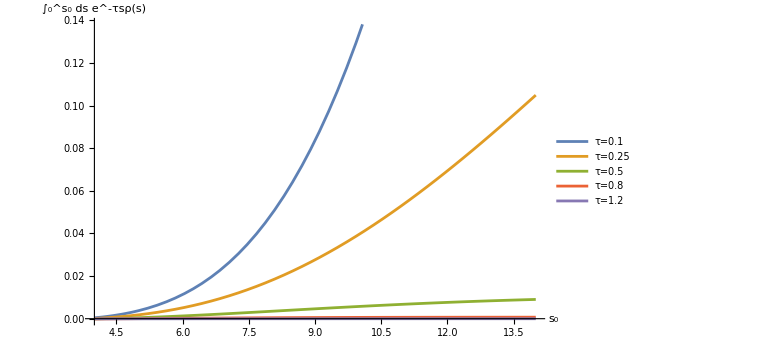

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for ρ_6=ρ_8=ρ_10=1

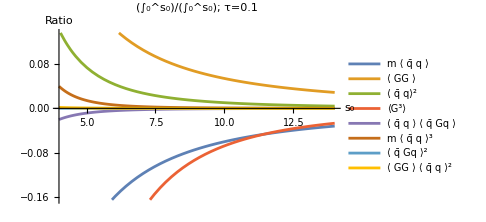
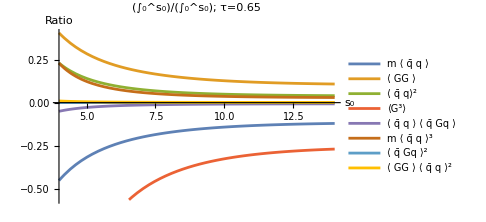
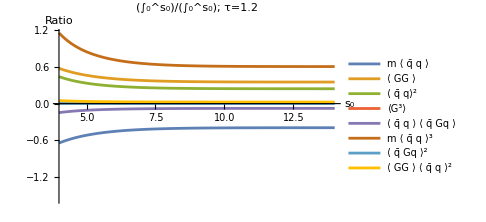

```mathematica
(*-------------------------------*)
```

ℛ^0 for ρ_6=ρ_8=ρ_10=1

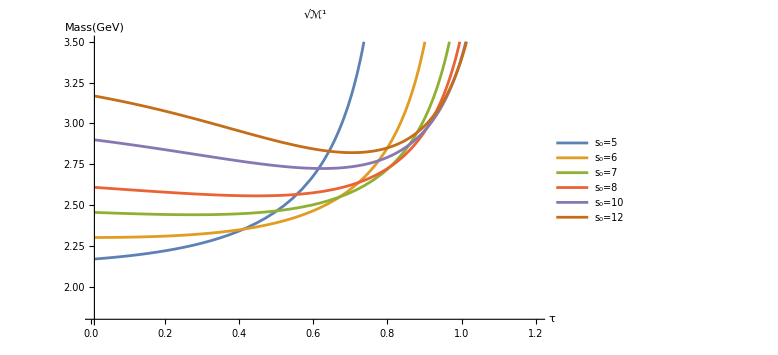
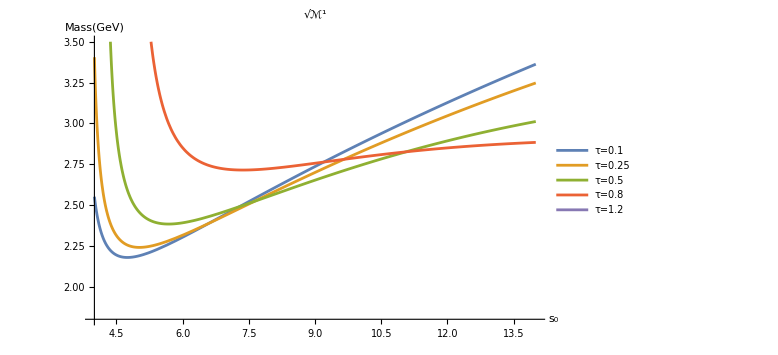

```mathematica
(*-------------------------------*)
```

ℛ^1 for ρ_6=ρ_8=ρ_10=1

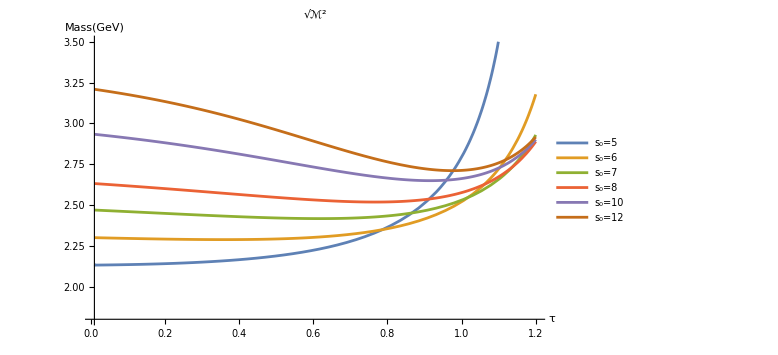
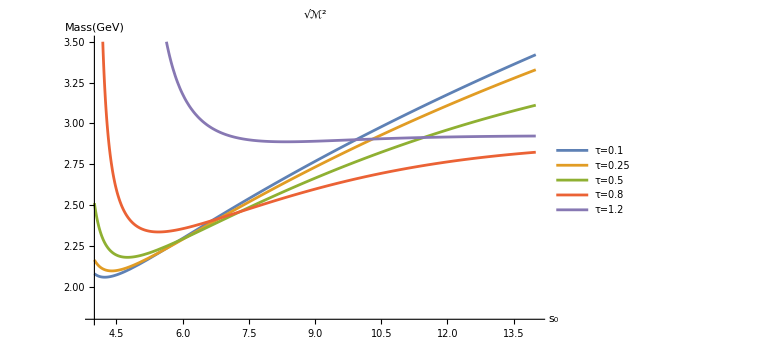

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for ρ_6=3, ρ_8=5, ρ_10=5

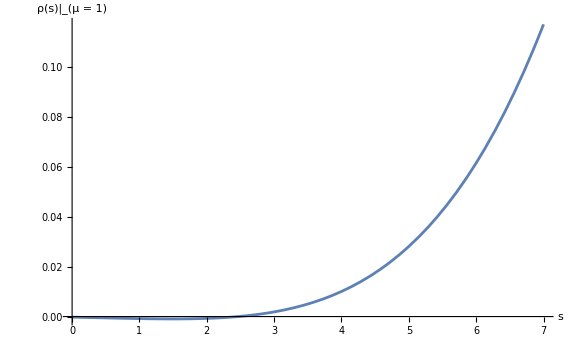
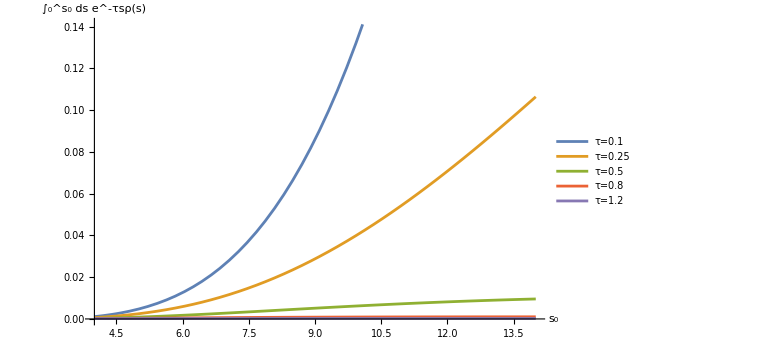

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for ρ_6=3, ρ_8=5, ρ_10=5

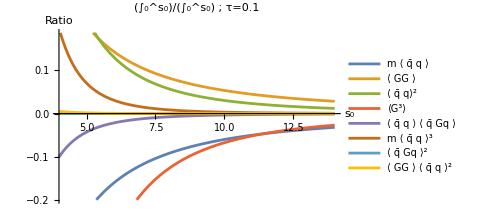
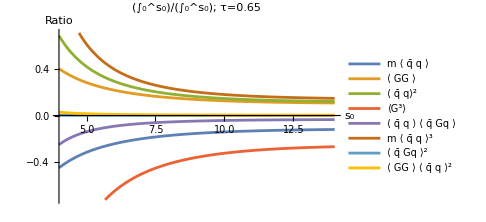
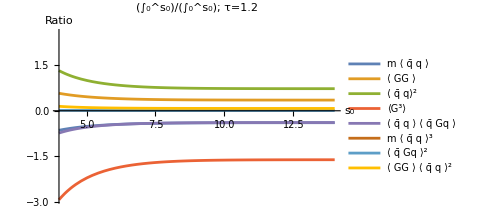

```mathematica
(*-------------------------------*)
```

ℛ^0 for ρ_6=3, ρ_8=5, ρ_10=5

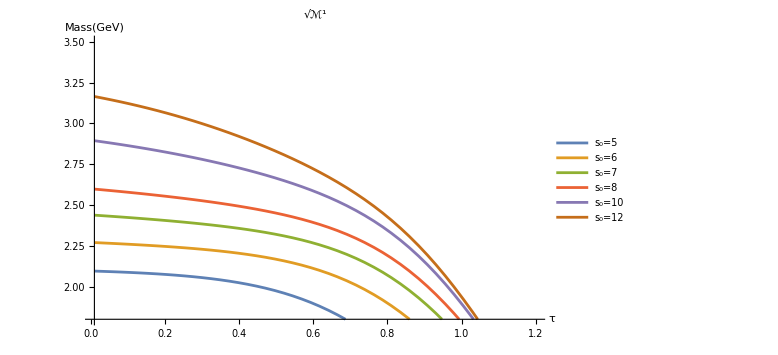
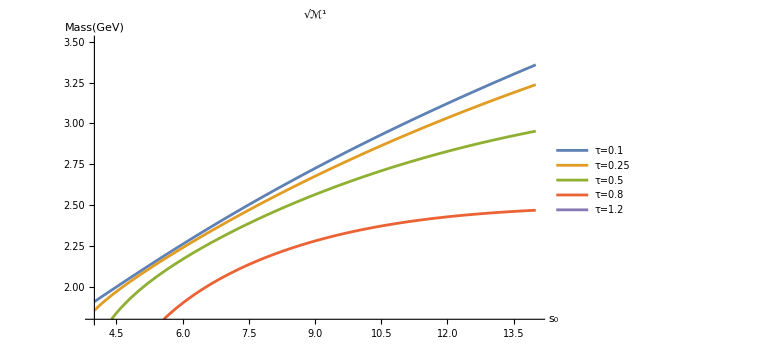

```mathematica
(*-------------------------------*)
```

ℛ^1 for ρ_6=3, ρ_8=5, ρ_10=5